```mathematica
rawdata=Import["~/montecarloPi/data3.csv"][[All,2;;3]];
rawdata=Table[{rawdata[[x,2]],rawdata[[x,1]]},{x,1,Length[rawdata]}]
```

{{1,75.8641},{1,76.1954},{1,73.809},{2,67.4703},{2,64.0395},{4,42.488},{4,45.8576}}

#### Linear Fit

```mathematica
avgPoints={
{1,Total[rawdata[[1;;3,2]]/Length[rawdata[[1;;3,2]]]]},
{2,Total[rawdata[[4;;5,2]]/Length[rawdata[[4;;5,2]]]]},
{4,Total[rawdata[[6;;7,2]]/Length[rawdata[[6;;7,2]]]]}
};
```

```mathematica
lm = LinearModelFit[avgPoints,x,x];
Normal[lm]
```

86.0805-10.4321 x

```mathematica
Normal[lm]
```

86.0805-10.4321 x

```mathematica
avgPoints
```

{{1,75.2895},{2,65.7549},{4,44.1728}}

```mathematica
standardError[ts_]:=StandardDeviation[ts]/Abs[ts]
```

```mathematica
stderr=standardError[avgPoints[[All,2]]]
stderr=Table[{avgPoints[[i,1]],avgPoints[[i,2]],stderr[[i]]},{i,1,3}]
```

{0.211747,0.242451,0.360908}

{{1,75.2895,0.211747},{2,65.7549,0.242451},{4,44.1728,0.360908}}

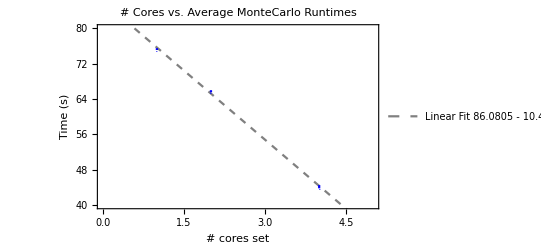

```mathematica
points=ListPlot[avgPoints,PlotRange->{{0,5},All},PlotMarkers->{Automatic,Small},PlotStyle->{Black,Opacity[0.5]}];

fit=Plot[lm[x],{x,0,5},PlotStyle->{Gray,Dashed},PlotLegends->{"Linear Fit\n"<>ToString[Normal[lm]], FontSize->12}];

Needs["ErrorBarPlots`"]
errplot=ErrorListPlot[stderr,PlotMarkers->{".",Tiny},PlotStyle->{Blue}];

final=Show[{fit,errplot(*,points*)},Frame->True,FrameLabel->{"# cores set","Time (s)"},LabelStyle->Bold,PlotLabel->"# Cores vs. Average MonteCarlo Runtimes",PlotRange->{All,{40,80}}]
```

```mathematica
Rasterize[final,ImageResolution->200]
```

-Graphics-